```mathematica
SetDirectory[NotebookDirectory[] <> ".."];
```

```mathematica
Load[name_] := Module[{f=Import[name,{"Real64"}]},
G = f⟦1⟧;
n = IntegerPart[f⟦2⟧];
f = Drop[f, 2];
frames = Transpose[ArrayReshape[f, {Length[f] / (n*4+2), n*4 + 2}]];
time = frames⟦1⟧;
dt = (time⟦#1⟧ - time⟦#1 - 1⟧)&/@Range[2, Length[time]];
energy = frames⟦2⟧;
bodies = Drop[Drop[frames, 2],4;;;;4];
frameN = Length[bodies⟦1⟧];
{Transpose[#1]&/@ArrayReshape[bodies, {n, 3, frameN}], time, energy, dt}
];
```

```mathematica
file = Load["test6.bin"];
```

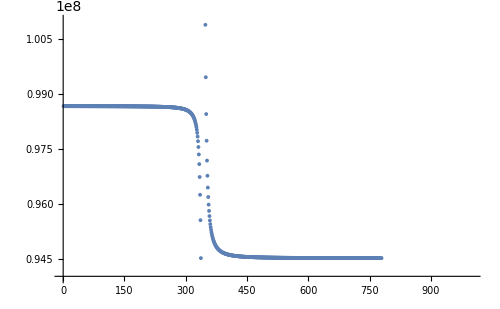

```mathematica
ListPlot[file⟦3⟧, ImageSize->500, PlotRange->{{0, 1000}, {9.4*10^7, 1.01*10^8}}]
```

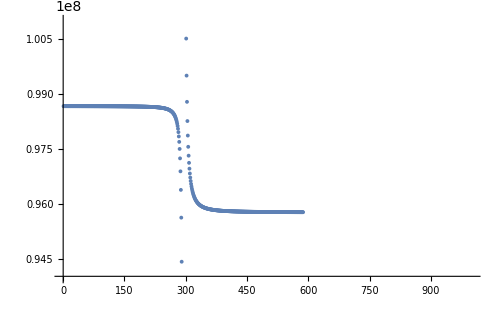

```mathematica
ListPlot[file⟦3⟧, ImageSize->500, PlotRange->{{0, 1000}, {9.4*10^7, 1.01*10^8}}]
```

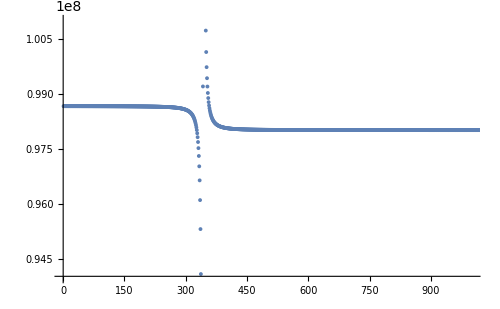

```mathematica
ListPlot[file⟦3⟧, ImageSize->500, PlotRange->{{0, 1000}, {9.4*10^7, 1.01*10^8}}]
```

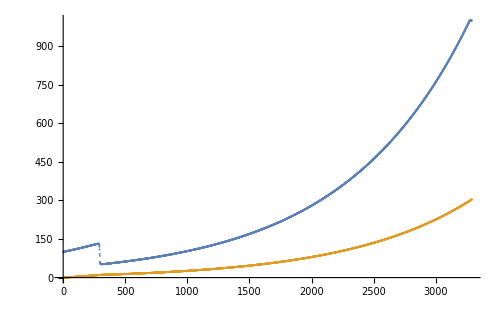

```mathematica
ListPlot[{file⟦4⟧, file⟦2⟧ / Length[file⟦2⟧]}, ImageSize->500, PlotRange->All]
```

```mathematica
ListPointPlot3D[file⟦1, ;;All, ;;200⟧, ImageSize->800, PlotStyle->PointSize[1/500], PlotRange->{{-4000, 4000}, {-4000,4000}, {-2000, 2000}}]
```

-Graphics3D-